```mathematica
(* Example Mathematica notebook code for Figure 2 in main text and Figure S1 in the Supplementary Information *)
(* Run using Mathematica version 12.0.0.0 on Mac OS X x86 (64-bit) *)
```

```mathematica
(* data imported from experimental data excel sheets *)

higherinitialconditionnomigration = {2.39377, 1.51369, 1.14735, 0.47369, 2.49454, 0.76274, 0.57631, 1.25570, 1.34172, 1.22551, 1.60789, 2.23239, 1.37371, 0.50162, 0.63781, 1.30435, 0.73043, 1.80534, 1.03469, 0.78220, 0.43733, 0.49330, 1.30027, 0.97121, 0.84218, 0.91317, 1.59545, 0.55012, 0.51091, 0.34625, 1.21076, 1.76268, 0.96154, 0.64933, 0.64516, 0.78631, 0.55104, 1.85067, 0.99338, 1.23726, 1.03416, 0.68254, 0.84447, 1.14089, 0.63919, 0.67566, 1.18698, 0.71986, 0.40925, 0.64750, 0.60132, 0.98285, 1.06809, 0.59370, 0.86177, 1.09183, 0.46746, 1.27002, 0.82245, 0.46062, 1.83409, 0.67794, 1.08898, 2.27798, 0.77337, 1.18307, 1.47399, 1.36439, 1.21906, 0.76019, 1.28218, 0.62479, 1.75637, 1.01315, 0.05836, 0.59401, 0.59880,1.44570, 0.66320, 1.01769, 1.31335, 0.79967, 2.01934, 0.44301, 1.24989, 1.38244, 0.85503, 0.99358};

higherinitialconditionwithmigration = {1.10041, 1.02266, 0.74952, 1.02796, 0.92545, 1.81106, 1.50193, 1.48144, 1.26322, 1.48856, 0.93090, 0.41372, 1.16449, 1.10825, 0.64351, 0.95324, 1.01317, 1.30741, 0.68738, 1.06726, 1.11971, 1.39197, 0.52273, 0.27978,1.13645, 0.73295, 0.65413, 1.13520, 1.07326, 1.35090, 0.93304, 0.82652, 1.54041, 1.38308, 0.38677, 0.16098,1.11469, 0.94450, 0.94488, 1.40161, 1.27255, 0.80082, 0.95125, 0.88834, 2.33832, 1.11290, 1.53599, 0.20558,0.769601, 1.133252, 1.316322, 1.149716, 0.959185, 0.988459, 0.960496, 0.844737, 1.982202, 1.215398, 1.727152, 1.163238,0.474450, 1.015689, 1.294070, 1.504382, 0.964320, 1.320331, 1.075994, 1.450351, 1.956826, 1.929771, 1.633575, 1.496052,0.338894, 1.005696, 1.347551, 1.242834, 1.030402, 1.634625, 1.431719, 1.554802, 0.910681, 1.378594, 1.300806, 1.280750,0.382237, 1.018698, 1.018633, 1.367658, 0.871286, 1.562374, 1.300002, 2.030591, 0.956778, 1.191908, 1.384061, 1.020015};

lowerinitialconditionnomigration ={0.006491, 0.016606, 0.237750, 0.010995, 0.178781, 0.192612, 0.011364, 0.106857, 0.075314, 0.030488, 0.211014, 0.481490, 0.004101, 0.000694, 0.589356, 0.088172, 0.037494, 0.060790, 0.055724, 0.101141, 0.011740, 0.007223, 0.050507, 0.190522, 0.122912, 0.021001, 0.090236, 0.191175, 0.053946, 0.870409, 0.026704, 0.159894, 0.004387, 0.044684, 0.120808, 0.030270,  0.071593, 0.368898, 0.151143, 0.104996, 0.024820, 0.069923, 0.064209, 0.090428, 0.014524, 0.003741, 0.001362, 0.026334, 0.879553, 0.013092, 0.046628, 0.038034, 0.094076, 0.189834, 0.046129, 0.025510, 0.099979, 0.333766, 0.070458, 0.004250, 0.035268, 0.036294, 0.000900, 0.078126, 0.039796, 0.001376, 0.000000, 0.074645, 0.014185, 0.285481, 0.345615, 0.383945, 0.201962, 0.555957, 0.065658, 0.005614, 0.051305, 0.006453, 0.003928, 0.041500, 0.070107, 0.071795, 0.152218, 0.022315, 0.366024, 0.048916, 0.130876, 0.009920, 0.092279, 0.017977, 0.019255, 0.051487, 0.000763, 0.128469, 0.000000, 0.060912};

lowerinitialconditionwithmigration ={0.011818, 0.003487, 0.058154, 0.087166, 0.026664, 0.092102, 0.031296, 0.025117, 0.075377, 0.183565, 0.012163, 0.048815, 0.010740, 0.013650, 0.117853, 0.050126, 0.019252, 0.025677, 0.014034, 0.151257, 0.045118, 0.287333, 0.051417, 0.091926, 0.065656, 0.060878, 0.162748, 0.011718, 0.014559, 0.069326, 0.012800, 0.189354, 0.087630, 0.104670, 0.050809, 0.051872, 0.086968, 0.031632, 0.285273, 0.017677, 0.023939, 0.137197, 0.002992, 0.142626, 0.088018, 0.080598, 0.098837, 0.001545, 0.049777, 0.021671, 0.806303, 0.043913, 0.004048, 0.283275, 0.007716, 0.048707, 0.046580, 0.092867, 0.096597, 0.017095, 0.036887, 0.008199, 0.725635, 0.245353, 0.026196, 0.353487, 0.067634, 0.087232, 0.019783, 0.107484, 0.044202, 0.057788, 0.039573, 0.007164, 0.086381, 0.121803, 0.013021, 0.247542, 0.108693, 0.069214, 0.033634, 0.367070, 0.014146, 0.102983, 0.062795, 0.006303, 0.051998, 0.153113, 0.001721, 0.187938, 0.126288, 0.104201, 0.017468, 0.370604, 0.006766, 0.076470};
```

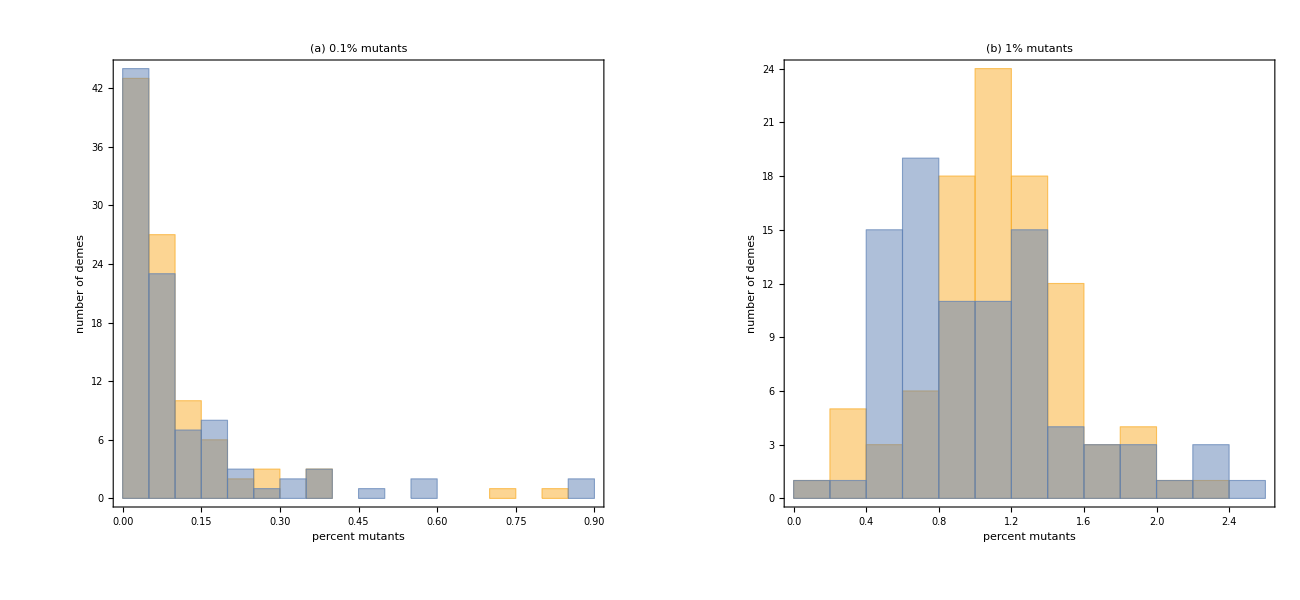

```mathematica
(* plot *)

lower = Histogram[{lowerinitialconditionwithmigration,lowerinitialconditionnomigration},Frame->True,ImageSize->{600,600},FrameStyle->Bold,FrameLabel->{"percent mutants","number of demes"},PlotRange->{Full,Full},PlotLabel->"(a) 0.1% mutants",AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}(*,ChartLegends->{"with migration","no migration"}*)];

higher = Histogram[{higherinitialconditionwithmigration,higherinitialconditionnomigration},Frame->True,ImageSize->{600,600},FrameStyle->Bold,FrameLabel->{"percent mutants","number of demes"},PlotRange->{Full,Full},PlotLabel->"(b) 1% mutants",AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}(*,ChartLegends->{"with migration","no migration"}*)];

GraphicsGrid[{{lower,higher}},ImageSize->{1300,600},AspectRatio->Full]
```